## Signature Functions

```mathematica
nrsign[d_,k_]:=If[d==1,k,(d^(k+1)-d)/(d-1)];
```

```mathematica
iterinteg[functions_,limits_,assumptions_]:=Fold[Integrate[#1*#2[[1]],#2[[2]],Assumptions->assumptions]&,1,Transpose[{functions,limits}]];
```

```mathematica
tensorfold[list_,dim_:2]:=If[Length[list]>=dim,ArrayReshape[list,ConstantArray[dim,Log[dim,Length[list]]]],list];
```

```mathematica
signat[paths_,limits_,level_:3]:=Module[{dpaths,dpathsf,integrands,ilimits,iassump,results},
dpaths=D[paths,t];
dpathsf=Map[Function[t,#]&,dpaths,{2}];
integrands=Table[Map[Tuples,Transpose[Table[Map[#[Subscript[t, j]]&,dpathsf,{2}],{j,1,k}]]],{k,1,level}];
ilimits=Table[Table[{Subscript[t, j],limits[[1]],If[j==k,limits[[2]],Subscript[t, j+1]]},{j,1,k}],{k,1,level}];
iassump=Fold[(#1&&(limits[[1]]<=Subscript[t, #2]<=limits[[2]]))&,(limits[[1]]<=Subscript[t, 1]<=limits[[2]]),Range[2,level]];
results=Table[Map[iterinteg[#,ilimits[[k]],iassump]&,integrands[[k]],{2}],{k,1,level}];
Map[tensorfold,Map[Prepend[#,{1}]&,Transpose[results]],{2}]
];
```

```mathematica
sigtake[sig_,index_]:=Module[{level,part},
level=Length[index];
part=Apply[Part,Join[{sig,level+1},index]];
If[index=={},1,part]];
```

```mathematica
signatline[betas_,index_,dt_:1]:=Module[{k},
k=Length[index];
(Apply[Times,Map[betas[[#]]&,index]]*(dt^k))/(k!)];
```

```mathematica
getcore6[sig_,level_:6]:=Module[{maxl},
maxl=Min[level,Length[sig]];
Join[
{{sigtake[sig,{1}],sigtake[sig,{2}]}},
If[maxl>=2,{{sigtake[sig,{1,2}]}},{}],
If[maxl>=3,{{sigtake[sig,{1,1,2}],sigtake[sig,{1,2,2}]}},{}],
If[maxl>=4,{{sigtake[sig,{1,1,1,2}],sigtake[sig,{1,1,2,2}],sigtake[sig,{1,2,2,2}]}},{}],
If[maxl>=5,{{sigtake[sig,{1,1,1,1,2}],sigtake[sig,{1,1,1,2,2}],sigtake[sig,{1,1,2,1,2}],sigtake[sig,{1,1,2,2,2}],sigtake[sig,{1,2,1,2,2}],sigtake[sig,{1,2,2,2,2}]}},{}],
If[maxl>=6,{{sigtake[sig,{1,1,1,1,1,2}],sigtake[sig,{1,1,1,1,2,2}],sigtake[sig,{1,1,1,2,1,2}],sigtake[sig,{1,1,1,2,2,2}],sigtake[sig,{1,1,2,1,2,2}],sigtake[sig,{1,1,2,2,1,2}],sigtake[sig,{1,1,2,2,2,2}],sigtake[sig,{1,2,1,2,2,2}],sigtake[sig,{1,2,2,2,2,2}]}},{}]]];
```

```mathematica
sigvarsubscr6[var_,level_:6,dim_:2]:=Take[{{1},
Table[vind[{i},var],{i,1,dim}],
tensorfold[Flatten[Table[vind[{i,j},var],{i,1,dim},{j,1,dim}]],dim],
tensorfold[Flatten[Table[vind[{i,j,k},var],{i,1,dim},{j,1,dim},{k,1,dim}]],dim],
tensorfold[Flatten[Table[vind[{i,j,k,l},var],{i,1,dim},{j,1,dim},{k,1,dim},{l,1,dim}]],dim],
tensorfold[Flatten[Table[vind[{i,j,k,l,m},var],{i,1,dim},{j,1,dim},{k,1,dim},{l,1,dim},{m,1,dim}]],dim],
tensorfold[Flatten[Table[vind[{i,j,k,l,m,n},var],{i,1,dim},{j,1,dim},{k,1,dim},{l,1,dim},{m,1,dim},{n,1,dim}]],dim]},level+1];
```

## Signatures

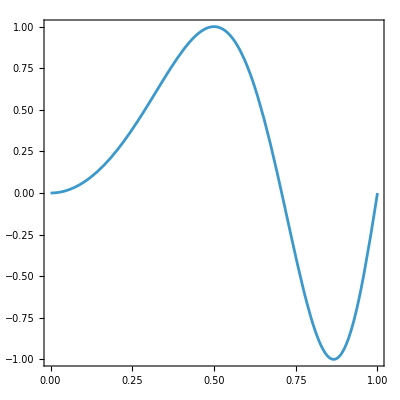

```mathematica
ParametricPlot[{t,Sin[2π t^2]},{t,0,1},Frame->True,PlotRange->All,AspectRatio->1]
```

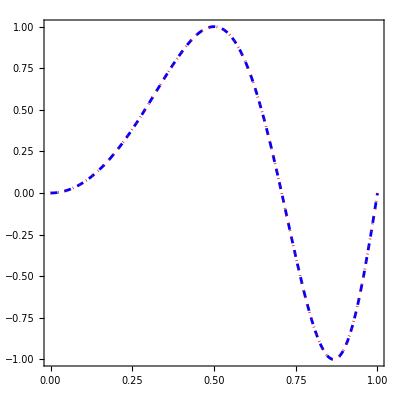

```mathematica
ParametricPlot[{{t,Sin[2π t^2]},{√t,Sin[2π t]}},{t,0,1},
Frame->True,PlotRange->All,AspectRatio->1,
PlotStyle->{{Blue,Dashed},{Red,Dotted}}]
```

```mathematica
Timing[{sigsinst2,sigsinst}=signat[{{t,Sin[2π t^2]},{√t,Sin[2π t]}},{0,1},4];]
```

{55.3958,Null}

```mathematica
sigsinst2==sigsinst
```

True

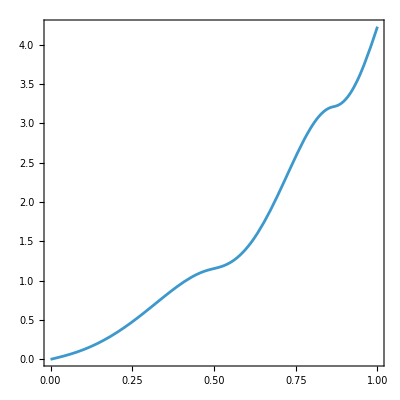

```mathematica
ParametricPlot[{t,ArcLength[Sin[2π x^2],{x,0,t}]},{t,0,1},Frame->True,PlotRange->All,AspectRatio->1]
```

```mathematica
l=N[ArcLength[Sin[2π t^2],{t,0,1}]]
```

4.22891

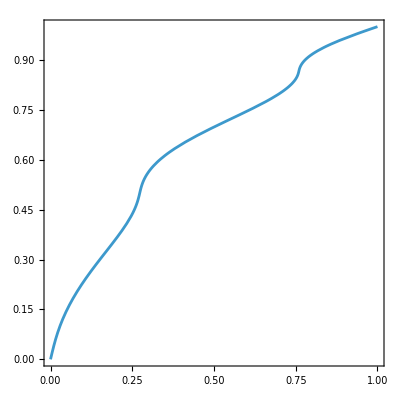

```mathematica
ParametricPlot[{ArcLength[Sin[2π x^2],{x,0,t}]/l,t},{t,0,1},Frame->True,PlotRange->All,AspectRatio->1]
```

## Functions

```mathematica
lineeq[{{x1_,y1_},{x2_,y2_}},var_]:=FullSimplify[y1+((y2-y1)/(x2-x1))(var-x1)];
```

```mathematica
lineeq[{{1,2},{2,4}},t]
```

2 t

```mathematica
approx[pts_,var_]:=Module[{n,conds,eqs},
n=Length[pts]-1;
conds=Table[pts[[j]][[1]]<=var<=pts[[j+1]][[1]],{j,1,n}];
eqs=Map[lineeq[#,var]&,Table[{pts[[j]],pts[[j+1]]},{j,1,n}]];
Piecewise[Transpose[{eqs,conds}]]
];
```

```mathematica
lineeqt[{{x1_,y1_},{x2_,y2_}},xt_]:=FullSimplify[{xt,y1+((y2-y1)/(x2-x1))(xt-x1)}];
```

```mathematica
lineeqt[{{1,2},{2,4}},t]
```

{t,2 t}

```mathematica
approxt[pts_,fxt_]:=Module[{n,conds,eqs},
n=Length[pts]-1;
conds=Table[pts[[j]][[1]]<=xt<=pts[[j+1]][[1]],{j,1,n}];
eqs=Map[lineeqt[#,xt]&,Table[{pts[[j]],pts[[j+1]]},{j,1,n}]];
Piecewise[Transpose[{eqs,conds}]]
];
```

```mathematica
pts4={{0,0},{0.12486596487113379,0.06868511481948694},{0.5096966711949104,1.100546753343191},{0.5302350641930077,1.1550883912306211},{0.8800206686529878,-1.2037657853746164},{1.0000055404764765,-1.0406736361545654*^-8}};
```

```mathematica
approx[pts4,t]
```

Piecewise[{{0.550071 t, 0≤t≤0.124866}, {-0.266123+2.68134 t, 0.124866≤t≤0.509697}, {-0.253001+2.65559 t, 0.509697≤t≤0.530235}, {4.73084-6.74371 t, 0.530235≤t≤0.880021}, {-10.0327+10.0326 t, 0.880021≤t≤1.00001}, {0, True}}]

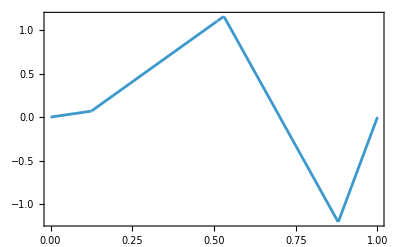

```mathematica
Plot[approx[pts4,t],{t,0,1},
Frame->True,PlotRange->All]
```

```mathematica
approxt[pts4,t]
```

Piecewise[{{{xt,0.550071 xt}, 0≤xt≤0.124866}, {{xt,-0.266123+2.68134 xt}, 0.124866≤xt≤0.509697}, {{xt,-0.253001+2.65559 xt}, 0.509697≤xt≤0.530235}, {{xt,4.73084-6.74371 xt}, 0.530235≤xt≤0.880021}, {{xt,-10.0327+10.0326 xt}, 0.880021≤xt≤1.00001}, {0, True}}]

```mathematica
ParametricPlot[approxt[pts4,t],{t,0,1},
AspectRatio->1/2,Frame->True,PlotRange->All]
```

-Graphics-

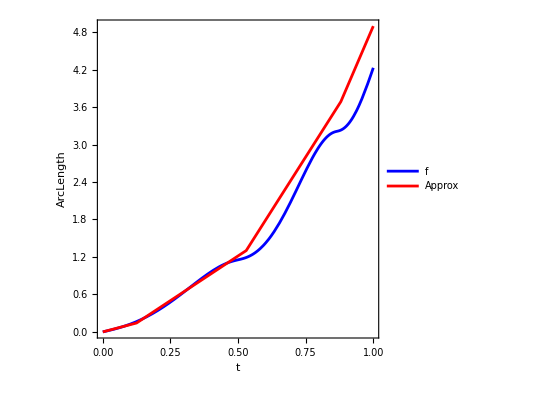

```mathematica
ParametricPlot[{
{t,ArcLength[Sin[2π x^2],{x,0,t}]},
{t,ArcLength[approx[pts4,x],{x,0,t}]}},
{t,0,1},Frame->True,PlotRange->All,AspectRatio->1,
PlotStyle->{Blue,Red},PlotLegends->{"f","Approx"},
FrameLabel->{"t","ArcLength"}]
```

```mathematica
la=N[ArcLength[approx[pts4,t],{t,0,1}]]
```

4.8964

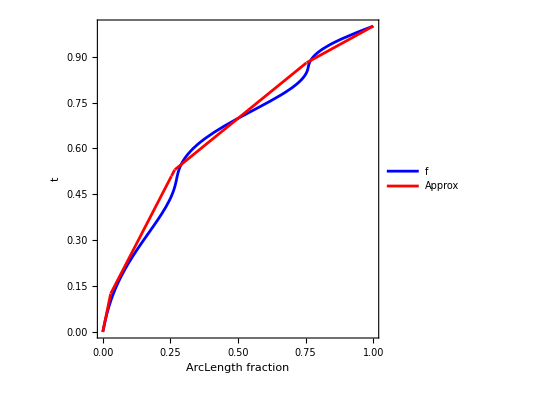

```mathematica
ParametricPlot[
{{ArcLength[Sin[2π x^2],{x,0,t}]/l,t},
{ArcLength[approx[pts4,x],{x,0,t}]/la,t}},
{t,0,1},Frame->True,PlotRange->All,AspectRatio->1,
PlotStyle->{Blue,Red},PlotLegends->{"f","Approx"},
FrameLabel->{"ArcLength fraction","t"}]
```

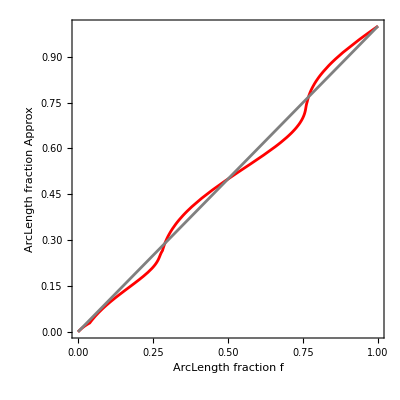

```mathematica
ParametricPlot[
{{ArcLength[Sin[2π x^2],{x,0,t}]/l,ArcLength[approx[pts4,x],{x,0,t}]/la},{t,t}},
{t,0,1},Frame->True,PlotRange->All,AspectRatio->1,
PlotStyle->{Red,Gray},
FrameLabel->{"ArcLength fraction f","ArcLength fraction Approx"}]
```

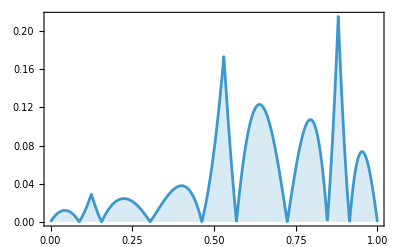

```mathematica
DiscretePlot[EuclideanDistance[{t,Sin[2π t^2]},{t,approx[pts4,t]}],
{t,0,1,10^-3},Frame->True,PlotRange->All]
```

```mathematica
mfdsig4=Mean[Table[EuclideanDistance[{t,Sin[2π t^2]},{t,approx[pts4,t]}],
{t,0,1,10^-3}]]
```

0.0474057

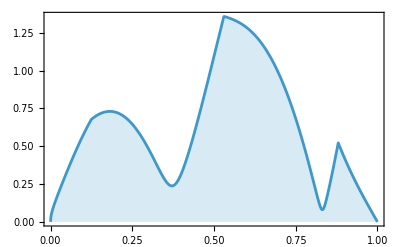

```mathematica
DiscretePlot[EuclideanDistance[{√t,Sin[2π t]},{t,approx[pts4,t]}],
{t,0,1,10^-3},Frame->True,PlotRange->All]
```

```mathematica
Mean[Table[EuclideanDistance[{√t,Sin[2π t]},{t,approx[pts4,t]}],
{t,0,1,10^-3}]]
```

0.624124

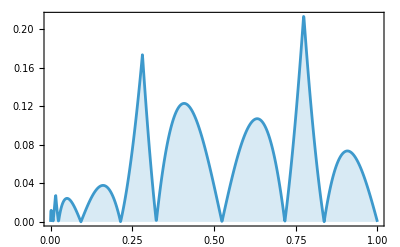

```mathematica
DiscretePlot[EuclideanDistance[{√t,Sin[2π t]},{√t,approx[pts4,√t]}],
{t,0,1,10^-3},Frame->True,PlotRange->All]
```

```mathematica
Mean[Table[EuclideanDistance[{√t,Sin[2π t]},{√t,approx[pts4,√t]}],
{t,0,1,10^-3}]]
```

0.0615053

```mathematica
approxt[pts4,√t]
```

Piecewise[{{{xt,0.550071 xt}, 0≤xt≤0.124866}, {{xt,-0.266123+2.68134 xt}, 0.124866≤xt≤0.509697}, {{xt,-0.253001+2.65559 xt}, 0.509697≤xt≤0.530235}, {{xt,4.73084-6.74371 xt}, 0.530235≤xt≤0.880021}, {{xt,-10.0327+10.0326 xt}, 0.880021≤xt≤1.00001}, {0, True}}]

```mathematica
DiscretePlot[EuclideanDistance[{√t,Sin[2π t]},approxt[pts4,√t]],
{t,0,1,10^-3},Frame->True,PlotRange->All]
```

-Graphics-

```mathematica
Mean[Table[EuclideanDistance[{√t,Sin[2π t]},approxt[pts4,√t]],
{t,0,1,10^-3}]]
```

```mathematica
tblrnd[rangex_,rangey_,n_,samples_,first_,last_]:=Map[Prepend[Append[#,last],first]&,Map[Sort,ArrayReshape[Transpose[{RandomReal[rangex,n samples],RandomReal[rangey,n samples]}],{samples,n,2}]]];
```

```mathematica
tblrnd[{0,1},{-2,2},3,10,{0,0},{1,0}]
```

{{{0,0},{0.0871751,0.11097},{0.317446,-1.66668},{0.503596,0.923276},{1,0}},{{0,0},{0.202832,-0.729648},{0.204178,0.48833},{0.351714,-0.839536},{1,0}},{{0,0},{0.669099,-0.20736},{0.708686,1.92758},{0.728987,0.0171292},{1,0}},{{0,0},{0.296271,-0.657922},{0.482929,1.4888},{0.853455,1.05401},{1,0}},{{0,0},{0.51778,-1.72399},{0.667579,0.695363},{0.875839,-1.43234},{1,0}},{{0,0},{0.278455,-0.0153795},{0.484887,-0.176487},{0.720551,-1.96065},{1,0}},{{0,0},{0.110732,1.92193},{0.37343,0.671969},{0.417531,-1.73017},{1,0}},{{0,0},{0.0115747,0.536449},{0.174506,-1.68853},{0.744853,-1.56325},{1,0}},{{0,0},{0.596575,1.38508},{0.67037,1.21586},{0.737861,-0.847466},{1,0}},{{0,0},{0.473677,1.7636},{0.501699,0.195277},{0.548624,-1.6908},{1,0}}}

```mathematica
meandist[f_,pts_,T_,step_]:=Mean[Table[EuclideanDistance[{t,f},{t,approx[pts,t]}],
{t,0,T,step}]];
```

```mathematica
meandist[Sin[2π t^2],pts4,1,10^-3]
```

0.0474057

```mathematica
T=1;
step=10^-3;
rangeX={0,T};
rangeY={-2,+2};
n=5-2;
first={0,0};
last={T,0};
```

```mathematica
popsize=250;
```

```mathematica
testtbl=tblrnd[rangeX,rangeY,n,popsize,first,last];
```

```mathematica
genpts[f_,T_,step_,rangex_,rangey_,n_,samples_,first_,last_]:=Module[{tbl},
tbl=tblrnd[rangex,rangey,n,samples,first,last];
SortBy[Map[{#,meandist[f,#,T,step]}&,tbl],Last]];
```

```mathematica
genpts[Sin[2π t^2],T,step,rangeX,rangeY,n,10,first,last]
```

{{{{0,0},{0.38474,0.285943},{0.461059,1.62274},{0.786675,-0.579149},{1,0}},0.225302},{{{0,0},{0.246808,-0.240107},{0.660437,-0.634773},{0.943408,-0.587603},{1,0}},0.665026},{{{0,0},{0.539007,0.536424},{0.716833,1.31176},{0.79085,1.84234},{1,0}},0.706944},{{{0,0},{0.11393,-0.862082},{0.257489,-1.41816},{0.361048,0.449571},{1,0}},0.726488},{{{0,0},{0.159943,1.74419},{0.243507,-0.0134591},{0.847523,0.596406},{1,0}},0.738012},{{{0,0},{0.138531,0.54254},{0.412747,0.232111},{0.610296,-1.71811},{1,0}},0.746611},{{{0,0},{0.0264038,1.58405},{0.504499,1.26179},{0.699689,0.495965},{1,0}},0.774733},{{{0,0},{0.30308,1.69818},{0.371464,-0.166596},{0.732636,1.18022},{1,0}},0.808601},{{{0,0},{0.115449,-1.46998},{0.365059,0.85878},{0.655221,-1.52315},{1,0}},0.814315},{{{0,0},{0.239931,-1.66507},{0.872031,-0.468522},{0.883778,1.73764},{1,0}},1.37412}}

```mathematica
Timing[testdists=SortBy[Map[{#,meandist[Sin[2π t^2],#,T,step]}&,testtbl],Last];]
```

{9.28312,Null}

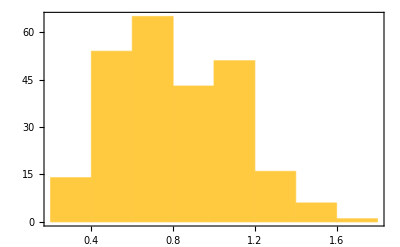

```mathematica
Histogram[Last[Transpose[testdists]],PlotRange->All,Frame->True]
```

```mathematica
Min[Last[Transpose[testdists]]]
```

0.270674

```mathematica
Take[testdists,5]
```

{{{{0,0},{0.395652,0.816054},{0.858963,-0.893802},{0.890452,-1.8358},{1,0}},0.270674},{{{0,0},{0.584814,0.787961},{0.668373,0.719728},{0.671286,0.0142088},{1,0}},0.295055},{{{0,0},{0.609096,1.06304},{0.840327,-0.716685},{0.928651,1.01306},{1,0}},0.296254},{{{0,0},{0.161486,-0.206136},{0.320567,1.62219},{0.83656,-0.756645},{1,0}},0.309241},{{{0,0},{0.425701,1.02779},{0.867329,0.242248},{0.950067,-1.16893},{1,0}},0.331083}}

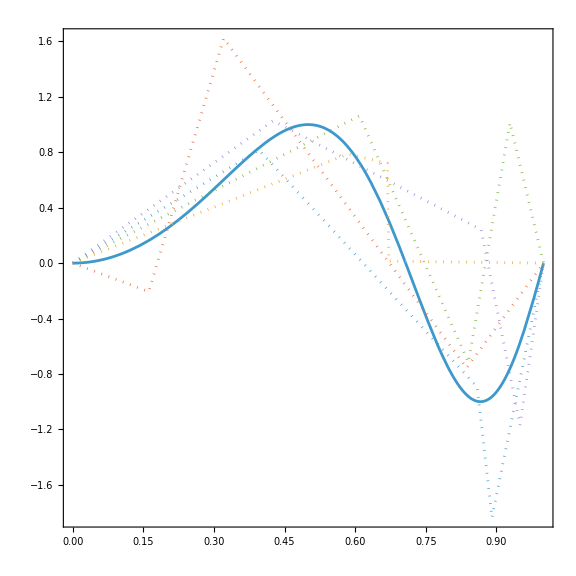

```mathematica
Show[ParametricPlot[{t,Sin[2π t^2]},{t,0,1},Frame->True,PlotRange->All,AspectRatio->1],
ListLinePlot[Map[First,Take[testdists,5]],
ImageSize->Large,Frame->True,PlotRange->All,PlotStyle->Dotted]]
```

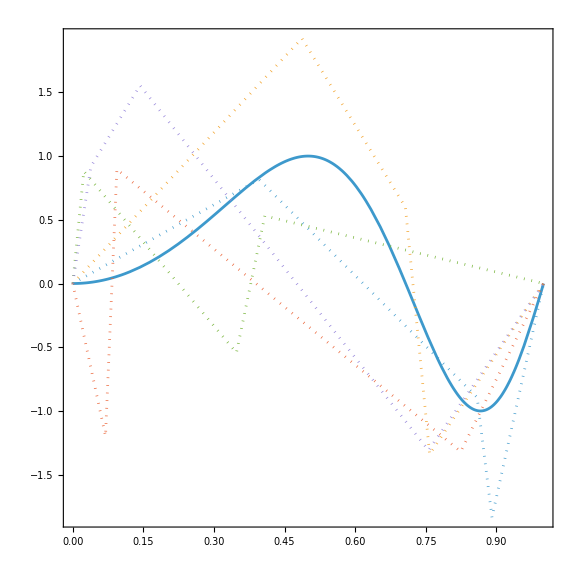

```mathematica
Show[ParametricPlot[{t,Sin[2π t^2]},{t,0,1},Frame->True,PlotRange->All,ImageSize->Large,AspectRatio->1],
ListLinePlot[Map[First,Part[testdists,{1,30,60,90,120}]],
ImageSize->Large,Frame->True,PlotRange->All,PlotStyle->Dotted]]
```

```mathematica
filterbounds[bump_,limitfirst_,limitlast_,eps_:0.5]:=Module[{newbump},
newbump=bump;
newbump[[1]][[1]]=Max[bump[[1]][[1]],eps*limitfirst];
newbump[[-1]][[1]]=Min[bump[[-1]][[1]],eps*limitlast];
newbump
]
```

```mathematica
mutate[pts_,σ_,copies_,eps_:0.5]:=Module[{first,mid,last,limitfirst,limitlast,bumps,newmid},
first=First[pts];
last=Last[pts];
mid=Rest[Most[pts]];
limitfirst=first[[1]]-First[mid][[1]];
limitlast=last[[1]]-Last[mid][[1]];
bumps=Table[RandomVariate[NormalDistribution[0,σ],Dimensions[mid]],{copies}];
bumps=Map[filterbounds[#,limitfirst,limitlast,eps]&,bumps];
newmid=Map[(mid+#)&,bumps];
Map[Prepend[Append[#,last],first]&,newmid]];
```

```mathematica
mutate[pts4,0.025,5,0.5]
```

{{{0,0},{0.148772,0.0334718},{0.49992,1.07057},{0.524302,1.12725},{0.863835,-1.19192},{1.00001,-1.04067×10^-8}},{{0,0},{0.14884,0.09373},{0.501649,1.08973},{0.484314,1.16564},{0.85935,-1.217},{1.00001,-1.04067×10^-8}},{{0,0},{0.129533,0.0834876},{0.521439,1.09118},{0.509641,1.13179},{0.851816,-1.20055},{1.00001,-1.04067×10^-8}},{{0,0},{0.107716,0.0929093},{0.515803,1.12411},{0.544607,1.18269},{0.90415,-1.19763},{1.00001,-1.04067×10^-8}},{{0,0},{0.136434,0.103986},{0.482079,1.14747},{0.508643,1.12442},{0.878542,-1.17252},{1.00001,-1.04067×10^-8}}}

```mathematica
next[sortedtbl_,best_,f_,T_,step_,rangex_,rangey_,n_,first_,last_,σ_,copies_,eps_:0.5,print_:False]:=Module[{elite,mutations,newgen,all,ans},
elite=First[Transpose[Take[sortedtbl,best]]];
mutations=Flatten[Map[mutate[#,σ,copies,eps]&,elite],1];
newgen=Map[First,genpts[f,T,step,rangex,rangey,n,Length[sortedtbl]-Length[elite]-Length[mutations],first,last]];
all=Join[elite,mutations,newgen];
ans=SortBy[Map[{#,meandist[f,#,T,step]}&,all],Last];
If[print,Print[First[ans]]];
ans
];
```

Ilhas e migração

```mathematica
(* next[sortedtbl_,islands_,best_,f_,T_,step_,rangex_,rangey_,n_,first_,last_,σ_,copies_,eps_:0.5,print_:False]:=Module[{elite,mutations,newgen,all,ans},
elite=First[Transpose[Take[sortedtbl,best]]];
mutations=Flatten[Map[mutate[#,σ,copies,eps]&,elite],1];
newgen=Map[First,genpts[f,T,step,rangex,rangey,n,Length[sortedtbl]-Length[elite]-Length[mutations],first,last]];
all=Join[elite,mutations,newgen];
ans=SortBy[Map[{#,meandist[f,#,T,step]}&,all],Last];
If[print,Print[First[ans]]];
ans
]; *)
```

```mathematica
(* Timing[poplist=NestList[next[#,10,Sin[2π t^2],1,10^-3,{0,1},{-2,+2},3,{0,0},{1,0},0.025,4,0.5]&,testdists,100];] *)
```

```mathematica
σ=0.025;
(* islands=5;
best=12; *)
best=60;
copies=2;
eps=0.5;
generations=50;
```

```mathematica
Timing[poplist=NestList[next[#,best,Sin[2π t^2],T,step,rangeX,rangeY,n,first,last,σ,copies,eps,True]&,testdists,generations];]
```

{{{0,0},{0.365698,0.288569},{0.537394,1.16505},{0.946702,-1.55997},{1,0}},0.175893}

{{{0,0},{0.357662,0.281283},{0.542011,1.16434},{0.929006,-1.59043},{1,0}},0.163532}

{{{0,0},{0.343409,0.287468},{0.531247,1.16544},{0.911634,-1.55109},{1,0}},0.146964}

{{{0,0},{0.320353,0.329998},{0.49945,1.18147},{0.91947,-1.53528},{1,0}},0.142361}

{{{0,0},{0.284752,0.296804},{0.52189,1.22338},{0.89166,-1.526},{1,0}},0.1202}

{{{0,0},{0.269949,0.307758},{0.546591,1.21824},{0.90661,-1.55036},{1,0}},0.101924}

{{{0,0},{0.269949,0.307758},{0.546591,1.21824},{0.90661,-1.55036},{1,0}},0.101924}

{{{0,0},{0.249058,0.297212},{0.560113,1.17493},{0.867312,-1.43848},{1,0}},0.0868886}

{{{0,0},{0.249058,0.297212},{0.560113,1.17493},{0.867312,-1.43848},{1,0}},0.0868886}

{{{0,0},{0.231351,0.326415},{0.558153,1.19047},{0.876125,-1.41919},{1,0}},0.0679457}

{{{0,0},{0.231351,0.326415},{0.558153,1.19047},{0.876125,-1.41919},{1,0}},0.0679457}

{{{0,0},{0.231351,0.326415},{0.558153,1.19047},{0.876125,-1.41919},{1,0}},0.0679457}

«2 more identical outputs»

{{{0,0},{0.218582,0.332346},{0.54468,1.21844},{0.889854,-1.36514},{1,0}},0.0670514}

{{{0,0},{0.215647,0.293031},{0.560387,1.24352},{0.873668,-1.41346},{1,0}},0.0666967}

{{{0,0},{0.196353,0.27771},{0.551792,1.20095},{0.865098,-1.35},{1,0}},0.0656926}

{{{0,0},{0.203234,0.244149},{0.540438,1.15846},{0.887137,-1.39769},{1,0}},0.0650339}

{{{0,0},{0.197334,0.202571},{0.56207,1.18572},{0.875454,-1.36023},{1,0}},0.064125}

{{{0,0},{0.182541,0.204751},{0.56234,1.18392},{0.870967,-1.38185},{1,0}},0.0592892}

{{{0,0},{0.182541,0.204751},{0.56234,1.18392},{0.870967,-1.38185},{1,0}},0.0592892}

{{{0,0},{0.173044,0.200866},{0.544418,1.15726},{0.878351,-1.31928},{1,0}},0.0532258}

{{{0,0},{0.173044,0.200866},{0.544418,1.15726},{0.878351,-1.31928},{1,0}},0.0532258}

{{{0,0},{0.173044,0.200866},{0.544418,1.15726},{0.878351,-1.31928},{1,0}},0.0532258}

«1 more identical outputs»

{{{0,0},{0.195179,0.233253},{0.547591,1.18182},{0.869428,-1.26271},{1,0}},0.0515638}

{{{0,0},{0.195179,0.233253},{0.547591,1.18182},{0.869428,-1.26271},{1,0}},0.0515638}

{{{0,0},{0.195179,0.233253},{0.547591,1.18182},{0.869428,-1.26271},{1,0}},0.0515638}

«5 more identical outputs»

{{{0,0},{0.170839,0.170632},{0.527022,1.18257},{0.873617,-1.20727},{1,0}},0.0495151}

{{{0,0},{0.170839,0.170632},{0.527022,1.18257},{0.873617,-1.20727},{1,0}},0.0495151}

{{{0,0},{0.170839,0.170632},{0.527022,1.18257},{0.873617,-1.20727},{1,0}},0.0495151}

«1 more identical outputs»

{{{0,0},{0.156682,0.137058},{0.530755,1.16876},{0.885968,-1.22653},{1,0}},0.0484787}

{{{0,0},{0.136251,0.0995053},{0.550651,1.19148},{0.878709,-1.26589},{1,0}},0.0481912}

{{{0,0},{0.136251,0.0995053},{0.550651,1.19148},{0.878709,-1.26589},{1,0}},0.0481912}

{{{0,0},{0.136251,0.0995053},{0.550651,1.19148},{0.878709,-1.26589},{1,0}},0.0481912}

«1 more identical outputs»

{{{0,0},{0.138477,0.109019},{0.543169,1.18297},{0.866714,-1.25834},{1,0}},0.0476752}

{{{0,0},{0.138477,0.109019},{0.543169,1.18297},{0.866714,-1.25834},{1,0}},0.0476752}

{{{0,0},{0.156012,0.139106},{0.547966,1.18083},{0.871395,-1.23411},{1,0}},0.0469444}

{{{0,0},{0.152454,0.122047},{0.53477,1.17839},{0.874908,-1.22768},{1,0}},0.0461329}

{{{0,0},{0.152454,0.122047},{0.53477,1.17839},{0.874908,-1.22768},{1,0}},0.0461329}

{{{0,0},{0.152454,0.122047},{0.53477,1.17839},{0.874908,-1.22768},{1,0}},0.0461329}

«2 more identical outputs»

{604.939,Null}

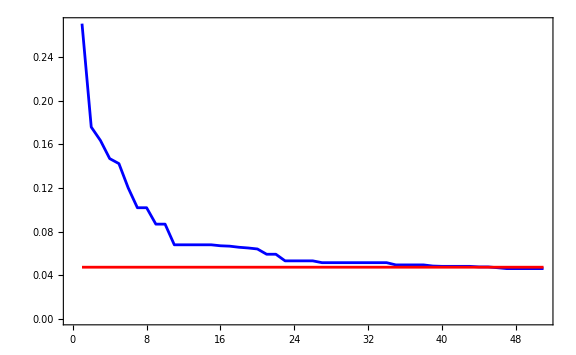

```mathematica
Show[
ListLinePlot[Map[Last[First[#]]&,poplist],
Frame->True,PlotRange->All,ImageSize->Large,PlotStyle->Blue],
Plot[mfdsig4,{t,1,Length[poplist]},PlotStyle->Red]]
```

```mathematica
Take[Last[poplist],5]
```

{{{{0,0},{0.152454,0.122047},{0.53477,1.17839},{0.874908,-1.22768},{1,0}},0.0461329},{{{0,0},{0.156012,0.139106},{0.547966,1.18083},{0.871395,-1.23411},{1,0}},0.0469444},{{{0,0},{0.145792,0.128013},{0.546365,1.16546},{0.876563,-1.22219},{1,0}},0.0475618},{{{0,0},{0.160439,0.141316},{0.532219,1.21306},{0.880927,-1.233},{1,0}},0.0476261},{{{0,0},{0.138477,0.109019},{0.543169,1.18297},{0.866714,-1.25834},{1,0}},0.0476752}}

```mathematica
pts4
```

{{0,0},{0.124866,0.0686851},{0.509697,1.10055},{0.530235,1.15509},{0.880021,-1.20377},{1.00001,-1.04067×10^-8}}

```mathematica
mfdsig4
```

0.0474057

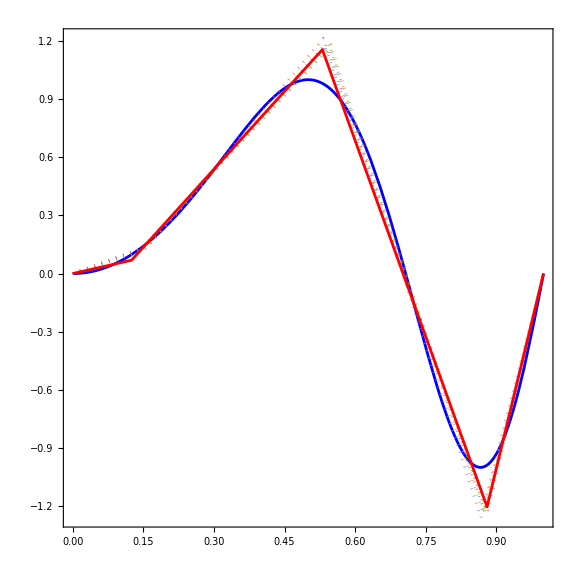

```mathematica
Show[ParametricPlot[{t,Sin[2π t^2]},{t,0,1},
Frame->True,PlotRange->All,AspectRatio->1,
ImageSize->Large,PlotStyle->Blue],
ListLinePlot[Take[Map[First,Last[poplist]],5],
PlotStyle->Dotted],
ListLinePlot[pts4,PlotStyle->Red]]
```